```mathematica
x=.
aug[1]=-0.298418430825675;
aug[2]=5.543570710335685*^-002;
aug[3]=-5.246873477196695*^-003;
avu=0.289981320042550;
bvu=5.00000348856006;
bvd=0.399728970464133;
lan=0.299822509305501;
aa=0;
bb=0;
cc=0;
aaaa=0;
bbbb=0;
cccc=0;
(*chi2=5634.98533807645
n_dof=774
chi2/n_dof=7.28034281405227*)
```

2.

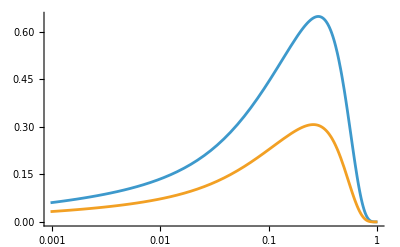

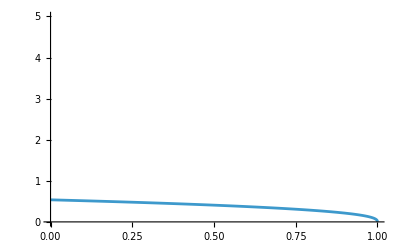

19.7046 ((2.70403 Gamma[0.289981+1. s])/Gamma[6.28998+1. s]+(59.8191 Gamma[1.28998+1. s])/Gamma[7.28998+1. s]-(34.4723 Gamma[2.28998+1. s])/Gamma[8.28998+1. s]+(581.777 Gamma[3.28998+1. s])/Gamma[9.28998+1. s])

10.5882 ((5.42423 Gamma[0.289981+1. s])/Gamma[6.68971+1. s]+(119.996 Gamma[1.28998+1. s])/Gamma[7.68971+1. s]-(69.1509 Gamma[2.28998+1. s])/Gamma[8.68971+1. s]+(1167.03 Gamma[3.28998+1. s])/Gamma[9.68971+1. s])

```mathematica
aaa =2/((Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvu])/Gamma[1+avu+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvu])/Gamma[2+avu+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvu])/Gamma[3+avu+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvu])/Gamma[4+avu+bvu]);
xuvgegn=aaa x^avu(1-x)^bvu(1+∑_(i=1)^3 aug[i]GegenbauerC[i,7/2,1-2x]);


bbb=1/ ((Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(7 aug[1] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(28 aug[2] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]+(84 aug[3] Gamma[avu] Gamma[1+bvd+bvu])/Gamma[1+avu+bvd+bvu]-(14 aug[1] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(126 aug[2] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]-(630 aug[3] Gamma[1+avu] Gamma[1+bvd+bvu])/Gamma[2+avu+bvd+bvu]+(126 aug[2] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]+(1386 aug[3] Gamma[2+avu] Gamma[1+bvd+bvu])/Gamma[3+avu+bvd+bvu]-(924 aug[3] Gamma[3+avu] Gamma[1+bvd+bvu])/Gamma[4+avu+bvd+bvu]);


xdvgegen=bbb x^avu(1-x)^bvu(1-x)^bvd(1+∑_(i=1)^3 aug[i]GegenbauerC[i,7/2,1-2x]);
NIntegrate[xuvgegn/x,{x,0,1}]
LogLinearPlot[{xuvgegn,xdvgegen},{x,0,1}]
Plot[{xdvgegen/xuvgegn},{x,0,1},PlotRange->{Automatic,{0,5}}]
x=Exp[-v];

Un=LaplaceTransform[xuvgegn,v,s]

Dn=LaplaceTransform[xdvgegen,v,s]
```

```mathematica
Λ=lan^2;
Q0=1;

β0=11-2/3 f;
β1=102-38/3 f;
"Q=Input["Q"]"; 
αQ=4Pi(1/(β0*(y-Log[Λ]))-β1/(β0)^3 Log[y-Log[Λ]]/(y-Log[Λ])^2);
αQ0=4Pi(1/(β0*(y0-Log[Λ]))-β1/(β0)^3 Log[y0-Log[Λ]]/(y0-Log[Λ])^2);

AlfasQ=αQ;
AlfasQ0=αQ0;
(*αQ=4Pi(1/(β0*(y-Log[Λ])));
αQ0=4Pi(1/(β0*(y0-Log[Λ])));*)
taQ=Integrate[1/(4Pi)AlfasQ,y]/.y->Log[Q];
taQ0=Integrate[1/(4Pi)AlfasQ0,y0]/.y0->Log[Q0];
ta=taQ-taQ0;
cf=4/3;
ca=3;
 tf=f;
tr=1/2;
(*lan=0.2*)
ta2n=(1/(β0^6))(-((2 β1^2)/(27 (Log[Q]-Log[Λ])^3))+(β0^2 β1)/(2 (Log[Q]-Log[Λ])^2)-β0^4/(Log[Q]-Log[Λ])+(β1 (-2 β1+9 β0^2 (Log[Q]-Log[Λ])) Log[Log[Q]-Log[Λ]])/(9 (Log[Q]-Log[Λ])^3)-(β1^2 Log[Log[Q]-Log[Λ]]^2)/(3 (Log[Q]-Log[Λ])^3))-(1/(β0^6))(-((2 β1^2)/(27 (Log[Q0]-Log[Λ])^3))+(β0^2 β1)/(2 (Log[Q0]-Log[Λ])^2)-β0^4/(Log[Q0]-Log[Λ])+(β1 (-2 β1+9 β0^2 (Log[Q0]-Log[Λ])) Log[Log[Q0]-Log[Λ]])/(9 (Log[Q0]-Log[Λ])^3)-(β1^2 Log[Log[Q0]-Log[Λ]]^2)/(3 (Log[Q0]-Log[Λ])^3));

"Lo Input Spliting Function";



pqq0=4-8/3(1/(s+1)+1/(s+2)+2(EulerGamma+PolyGamma[0,s+1]));
```

```mathematica
ppsqq1=cf (-ca/2+cf) (-2/(1+s)^3-2/(1+s)^2+4/(1+s)+Pi^2/(3 (1+s))+2/(2+s)^3-2/(2+s)^2-8/(2+s)-Pi^2/(3 (2+s))+5/(3+s)-13/(9 (4+s))+25/(36 (5+s))-41/(100 (6+s))+4/(25 (7+s))-HarmonicNumber[1+s/2]-1/3 Pi^2 (-HarmonicNumber[1/2 (-1+s)]+HarmonicNumber[s/2])+HarmonicNumber[(1+s)/2]+4 (-HarmonicNumber[s/2]+HarmonicNumber[(1+s)/2])+4/9 (-HarmonicNumber[1+s/2]+HarmonicNumber[(3+s)/2])+1/4 (-HarmonicNumber[2+s/2]+HarmonicNumber[(3+s)/2])+4/25 (-HarmonicNumber[2+s/2]+HarmonicNumber[(5+s)/2])+1/(1+s)^3(-8+(1+s) Log[16]+2 (1+s) PolyGamma[0,1+s/2]-2 (1+s) PolyGamma[0,(1+s)/2]-(1+s)^2 PolyGamma[1,1+s/2]+(1+s)^2 PolyGamma[1,(1+s)/2])-1/(2+s)^3 0.9998400000000001 (16/(1+s)^2+(12 s)/(1+s)^2+(2+s) Log[16]-2 (2+s) PolyGamma[0,1+s/2]+2 (2+s) PolyGamma[0,(1+s)/2]+(2+s)^2 PolyGamma[1,1+s/2]-(2+s)^2 PolyGamma[1,(1+s)/2])-1/(3+s)^3 1.9702 (164/((1+s)^2 (2+s)^2)+(284 s)/((1+s)^2 (2+s)^2)+(188 s^2)/((1+s)^2 (2+s)^2)+(60 s^3)/((1+s)^2 (2+s)^2)+(8 s^4)/((1+s)^2 (2+s)^2)-4 (3+s) Log[2]-2 (3+s) PolyGamma[0,1+s/2]+2 (3+s) PolyGamma[0,(1+s)/2]+(3+s)^2 PolyGamma[1,1+s/2]-(3+s)^2 PolyGamma[1,(1+s)/2])-1/(4+s)^3 1.801 (2176/((1+s)^2 (2+s)^2 (3+s)^2)+(4392 s)/((1+s)^2 (2+s)^2 (3+s)^2)+(3504 s^2)/((1+s)^2 (2+s)^2 (3+s)^2)+(1408 s^3)/((1+s)^2 (2+s)^2 (3+s)^2)+(288 s^4)/((1+s)^2 (2+s)^2 (3+s)^2)+(24 s^5)/((1+s)^2 (2+s)^2 (3+s)^2)+4 (4+s) Log[2]-2 (4+s) PolyGamma[0,1+s/2]+2 (4+s) PolyGamma[0,(1+s)/2]+(4+s)^2 PolyGamma[1,1+s/2]-(4+s)^2 PolyGamma[1,(1+s)/2])-1/(5+s)^3 1.3242 (57328/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(146144 s)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(162160 s^2)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(103728 s^3)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(42144 s^4)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(11160 s^5)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(1880 s^6)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(184 s^7)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)+(8 s^8)/((1+s)^2 (2+s)^2 (3+s)^2 (4+s)^2)-4 (5+s) Log[2]-2 (5+s) PolyGamma[0,1+s/2]+2 (5+s) PolyGamma[0,(1+s)/2]+(5+s)^2 PolyGamma[1,1+s/2]-(5+s)^2 PolyGamma[1,(1+s)/2])-1/(6+s)^2 0.6348 (Log[16]-2 PolyGamma[0,4+s/2]+2 PolyGamma[0,(7+s)/2]+(6+s) PolyGamma[1,4+s/2]-(6+s) PolyGamma[1,(7+s)/2])+1/(7+s)^2 0.1398 (Log[16]+2 PolyGamma[0,4+s/2]-2 PolyGamma[0,(9+s)/2]-(7+s) PolyGamma[1,4+s/2]+(7+s) PolyGamma[1,(9+s)/2])+1/2 (-Zeta[3,1+s/2]+Zeta[3,(1+s)/2]));
%/.s->1//N
```

-0.0100705

```mathematica
pnsp1=cf tf (-2/(3 (1+s)^2)-2/(9 (1+s))-2/(3 (2+s)^2)+22/(9 (2+s))+(20 HarmonicNumber[s])/9+4/3 Zeta[2,1+s])+cf^2 (-1/(1+s)^3-5/(1+s)-1/(2+s)^3+2/(2+s)^2+5/(2+s)+1/(1+s)^2 2 (EulerGamma+1/(1+s)+PolyGamma[0,1+s]-(1+s) PolyGamma[1,2+s])+1/(2+s)^2 2 (EulerGamma+1/(2+s)+PolyGamma[0,2+s]-(2+s) PolyGamma[1,3+s])-4 (HarmonicNumber[s] PolyGamma[1,1+s]-1/2 PolyGamma[2,1+s])+3 Zeta[2,1+s])+ca cf (-1/(1+s)^3+5/(6 (1+s)^2)+53/(18 (1+s))-1/(2+s)^3+5/(6 (2+s)^2)-187/(18 (2+s))+Pi^2/(6 (1+s))+Pi^2/(6 (2+s))-(67 HarmonicNumber[s])/9+1/3 Pi^2 HarmonicNumber[s]-11/3 Zeta[2,1+s]+2 Zeta[3,1+s]);
%/.s->1//N
```

-29.3239+4.7268 f

```mathematica
pqq1p=ppsqq1+pnsp1;
```

```mathematica
c2nlo=cf (-9-(2 π^2)/3-2/(1+s)^2+6/(1+s)-2/(2+s)^2+4/(2+s)+3 (PolyGamma[0,s+1]+EulerGamma)+(2( PolyGamma[0,s+2]+EulerGamma))/(1+s)+(2( PolyGamma[0,s+3]+EulerGamma))/(2+s)+1/3 (π^2+6 (PolyGamma[0,s+1]+EulerGamma)^2-6 PolyGamma[1,1+s]+4 Zeta[2,1+s]));
%/.s->1//N
```

-1.84865

```mathematica
mns=(1+(ta)(-(β1 pqq0)/β0^2+pnsp1/β0))(taQ/taQ0)^(-pqq0/β0);
uvn=mns Un;
dvn=mns Dn;
```

```mathematica
mnsNLO=Exp[   ta  (pqq0+ta2n/ta pnsp1)];
mnsNLOm=mnsNLO;
mnsNLOp=Exp[   ta  (pqq0+ta2n/ta pqq1p)];
uvn=mnsNLO Un;
dvn=mnsNLO Dn;
```

```mathematica
F2p=(4/9 uvn+1/9dvn)(1+ta/(4 Pi) c2nlo  );
```

```mathematica
Needs["ErrorBarLogPlots`"]
x=.
Nmax=.
Nmax=9;
α=3;
β=0.5;
θ=√((k!(2  k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!x^β(1-x)^α)D[(x^(β+k)(1-x)^(α+k)), {x,k}];
ckj=√((k! (2 k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!)1/(j!)(Pochhammer[-k,j]Pochhammer[α+β+k+1,j]Pochhammer[β+j+1,k-j]);Momentg1NLOF2p=(F2p)/.s->j+1;

aαβ[k_]:=∑_(j=0)^k ckj*Momentg1NLOF2p;

F2pxQ=x^β(1-x)^α*(∑_(k=0)^Nmax θ*aαβ[k]);
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
NMC0p65={{1000,0.0214,0.006133333},{1200,0.023,0.006666667},{1500,0.016,0.006133333},{2000,0.0287,0.0088},{3000,0.0113,0.003733333},{5000,0.00721,0.003466667},{8000,0.0213,0.0088},{12000,0.017,0.008533333},{20000,0.0113,0.009066667}}
```

{{1000,0.0214,0.00613333},{1200,0.023,0.00666667},{1500,0.016,0.00613333},{2000,0.0287,0.0088},{3000,0.0113,0.00373333},{5000,0.00721,0.00346667},{8000,0.0213,0.0088},{12000,0.017,0.00853333},{20000,0.0113,0.00906667}}

```mathematica
SLAC0p65={{4.29,0.08284,0.00106066},{5.05,0.08061,0.002564781},{5.71,0.07099,0.001498933},{6.29,0.0695,0.001033247},{6.81,0.06728,0.00105119},{7.24,0.05886,0.004951858},{7.89,0.06348,0.000764853},{8.63,0.06127,0.00082134},{9.52,0.05772,0.001103902},{10.6,0.0566,0.000940319},{11.49,0.05412,0.001217949},{13.15,0.05258,0.000993227},{14.46,0.05074,0.001423025},{15.56,0.04928,0.001252398},{16.64,0.0465,0.001278632},{18.32,0.0449,0.002535271},{20.62,0.04222,0.002720294},{22.21,0.04451,0.002370084},{}}
```

{{4.29,0.08284,0.00106066},{5.05,0.08061,0.00256478},{5.71,0.07099,0.00149893},{6.29,0.0695,0.00103325},{6.81,0.06728,0.00105119},{7.24,0.05886,0.00495186},{7.89,0.06348,0.000764853},{8.63,0.06127,0.00082134},{9.52,0.05772,0.0011039},{10.6,0.0566,0.000940319},{11.49,0.05412,0.00121795},{13.15,0.05258,0.000993227},{14.46,0.05074,0.00142303},{15.56,0.04928,0.0012524},{16.64,0.0465,0.00127863},{18.32,0.0449,0.00253527},{20.62,0.04222,0.00272029},{22.21,0.04451,0.00237008},{}}

```mathematica
BCDMC0p65={{13.25,0.04389,0.005151398},{15,0.04264,0.004367745},{17,0.04143,0.003946657},{19,0.04204,0.003578827},{21.5,0.04048,0.003067898},{24.5,0.04015,0.002321314},{28,0.03829,0.002051195},{32.5,0.03738,0.002199204},{37.5,0.03653,0.002044358},{43,0.03545,0.001935975},{49.5,0.03474,0.00172154},{57,0.03307,0.001475974},{65.5,0.03198,0.001267793},{75,0.03212,0.001186971},{86,0.03227,0.001266215},{99,0.03151,0.001232274},{115.5,0.02861,0.001171367},{137.5,0.02878,0.001218524},{175,0.02724,0.00196023},{230,0.02965,0.002524143},{}}
```

{{13.25,0.04389,0.0051514},{15,0.04264,0.00436775},{17,0.04143,0.00394666},{19,0.04204,0.00357883},{21.5,0.04048,0.0030679},{24.5,0.04015,0.00232131},{28,0.03829,0.0020512},{32.5,0.03738,0.0021992},{37.5,0.03653,0.00204436},{43,0.03545,0.00193598},{49.5,0.03474,0.00172154},{57,0.03307,0.00147597},{65.5,0.03198,0.00126779},{75,0.03212,0.00118697},{86,0.03227,0.00126622},{99,0.03151,0.00123227},{115.5,0.02861,0.00117137},{137.5,0.02878,0.00121852},{175,0.02724,0.00196023},{230,0.02965,0.00252414},{}}

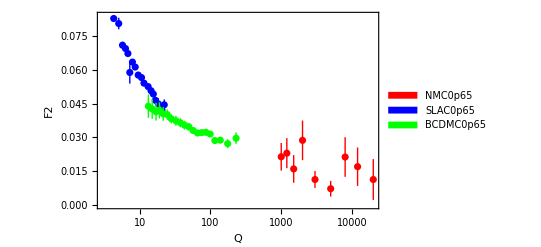

```mathematica
Needs["ErrorBarLogPlots`"]


fig1=ErrorListLogLinearPlot[{NMC0p65,SLAC0p65,BCDMC0p65},PlotRange->All,Frame->True,FrameLabel->{"Q","F2"},PlotStyle->{Directive[Thick,Red],Directive[Thick,Blue],Directive[Thick,Green]}];

Legended[fig1,Placed[SwatchLegend[{Directive[Thick,Red],Directive[Thick,Blue],Directive[Thick,Green]},{"NMC0p65","SLAC0p65","BCDMC0p65"}],{Right,Top}]]
```

```mathematica
M2[s_,Q_]:=F2p;


M2TMC[s_,Q_,mN_]:=M2[s,Q]+(s*(s-1))/(s+2)*(mN^2/Q)^1*M2[s+2,Q]+(Gamma[s+3]^2/(2*Gamma[s-1]*Gamma[s+5]))*(mN^2/Q)^2*M2[s+4,Q];
```

```mathematica
Needs["ErrorBarLogPlots`"]
x=.
mN=0.938
Nmax=.
Nmax=9;
α=3;
β=0.5;
θ=√((k!(2  k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!x^β(1-x)^α)D[(x^(β+k)(1-x)^(α+k)), {x,k}];
ckj=√((k! (2 k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!)1/(j!)(Pochhammer[-k,j]Pochhammer[α+β+k+1,j]Pochhammer[β+j+1,k-j]);Momentg1NLOF2pTMC=(M2TMC[s,Q,mN])/.s->j+1;

aαβTMC[k_]:=∑_(j=0)^k ckj*Momentg1NLOF2pTMC;

F2pxQTMC=x^β(1-x)^α*(∑_(k=0)^Nmax θ*aαβTMC[k]);
```

0.938

```mathematica
F2th=F2pxQTMC(1+aa(x^bb/((1-x))+cc)/Q);
```

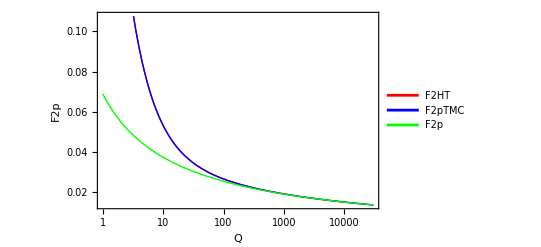

```mathematica
fig44=LogLinearPlot[{F2th/. x->0.65/. f->4,F2pxQTMC/. x->0.65/. f->4,F2pxQ/. x->0.65/. f->4},{Q,1,30000},Frame->True,FrameLabel->{"Q","F2p"},PlotStyle->{Directive[Thick,Red],Directive[Thick,Blue],Directive[Thick,Green]},PlotLegends->Placed[{"F2HT","F2pTMC","F2p"},{Right,Top}]]
```

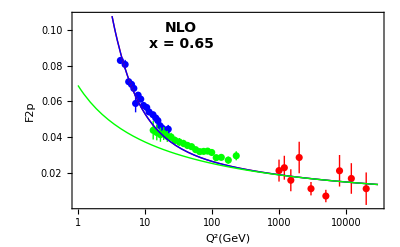

```mathematica
Show[fig1,fig44,PlotRange->All];
Legended[Show[fig1,fig44,PlotRange->All,Frame->True,FrameLabel->{"\!\(\*SuperscriptBox[\(Q\), \(2\)]\)(GeV)","F2p"},Epilog->{Text[Style["NLO",14,Bold],Scaled[{0.35,0.92}]],Text[Style["x = 0.65",14,Bold],Scaled[{0.35,0.84}]]}],Placed[SwatchLegend[{Directive[Thick,Red],Directive[Thick,Blue],Directive[Thick,Green]},{"NMC0p65","SLAC0p65","BCDMC0p65"}],{Right,Top}]]
```

```mathematica
F2d=5/18( uvn+dvn)(1+ta/(4 Pi) c2nlo  );
```

```mathematica
M2d[s_,Q_]:=F2d;


M2TMCd[s_,Q_,mNd_]:=M2d[s,Q]+(s*(s-1))/(s+2)*(mNd^2/Q)^1*M2d[s+2,Q]+(Gamma[s+3]^2/(2*Gamma[s-1]*Gamma[s+5]))*(mNd^2/Q)^2*M2d[s+4,Q];
```

```mathematica
Needs["ErrorBarLogPlots`"]
x=.
mNd=0.938
Nmax=.
Nmax=9;
α=3;
β=0.5;
θ=√((k!(2  k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!x^β(1-x)^α)D[(x^(β+k)(1-x)^(α+k)), {x,k}];
ckj=√((k! (2 k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!)1/(j!)(Pochhammer[-k,j]Pochhammer[α+β+k+1,j]Pochhammer[β+j+1,k-j]);Momentg1NLOF2dTMC=(M2TMCd[s,Q,mNd])/.s->j+1;

aαβTMC[k_]:=∑_(j=0)^k ckj*Momentg1NLOF2dTMC;

F2dxQTMC=x^β(1-x)^α*(∑_(k=0)^Nmax θ*aαβTMC[k]);
```

0.938

```mathematica
Needs["ErrorBarLogPlots`"]
x=.
Nmax=.
Nmax=9;
α=3;
β=0.5;
θ=√((k!(2  k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!x^β(1-x)^α)D[(x^(β+k)(1-x)^(α+k)), {x,k}];
ckj=√((k! (2 k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!)1/(j!)(Pochhammer[-k,j]Pochhammer[α+β+k+1,j]Pochhammer[β+j+1,k-j]);Momentg1NLOF2d=(F2d)/.s->j+1;

aαβd[k_]:=∑_(j=0)^k ckj*Momentg1NLOF2d;

F2dxQ=x^β(1-x)^α*(∑_(k=0)^Nmax θ*aαβd[k]);
```

```mathematica
F2thd=F2dxQTMC(1+aaaa(x^bbbb/((1-x))+cccc)/Q);
```

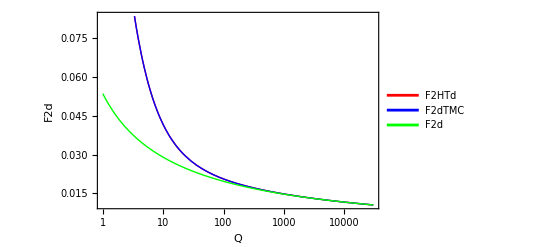

```mathematica
fig55=LogLinearPlot[{F2thd/. x->0.65/. f->4,F2dxQTMC/. x->0.65/. f->4,F2dxQ/. x->0.65/. f->4},{Q,1,30000},Frame->True,FrameLabel->{"Q","F2d"},PlotStyle->{Directive[Thick,Red],Directive[Thick,Blue],Directive[Thick,Green]},PlotLegends->Placed[{"F2HTd","F2dTMC","F2d"},{Right,Top}]]
```

```mathematica
SLACf2d={{4.15,0.06204,0.00085703},{4.41,0.05975,0.001925097},{5.01,0.05575,0.001720029},{5.72,0.05284,0.00229421},{6.27,0.05018,0.001145513},{6.78,0.04943,0.000756637},{7.98,0.04493,0.001797443},{8.61,0.04346,0.001359485},{9.75,0.04185,0.001196704},{10.6,0.04074,0.000868332},{11.53,0.03871,0.001340149},{13.17,0.03788,0.001966571},{14.2,0.03804,0.001017693},{15.24,0.03529,0.001315295},{16.89,0.03414,0.001436001},{18.28,0.03277,0.00158354},{20.63,0.03437,0.00161756},{22.21,0.03234,0.002641685}}
```

{{4.15,0.06204,0.00085703},{4.41,0.05975,0.0019251},{5.01,0.05575,0.00172003},{5.72,0.05284,0.00229421},{6.27,0.05018,0.00114551},{6.78,0.04943,0.000756637},{7.98,0.04493,0.00179744},{8.61,0.04346,0.00135949},{9.75,0.04185,0.0011967},{10.6,0.04074,0.000868332},{11.53,0.03871,0.00134015},{13.17,0.03788,0.00196657},{14.2,0.03804,0.00101769},{15.24,0.03529,0.0013153},{16.89,0.03414,0.001436},{18.28,0.03277,0.00158354},{20.63,0.03437,0.00161756},{22.21,0.03234,0.00264169}}

```mathematica
BCMCDf2d={{17,0.02807,0.003542654},{19,0.02869,0.003341138},{21.5,0.02673,0.002843976},{24.5,0.02861,0.002861625},{28,0.0237,0.002213527},{32.5,0.02494,0.00185809},{37.5,0.02526,0.001751371},{43,0.02382,0.001651969},{49.5,0.0247,0.001538473},{57,0.02343,0.001273185},{65.5,0.02224,0.001097133},{75,0.02278,0.001092245},{86,0.02076,0.001058159},{99,0.02218,0.001144945},{115.5,0.01993,0.001177455},{137.5,0.01965,0.001307708},{175,0.01814,0.002402769},{230,0.01605,0.002640928}}
```

{{17,0.02807,0.00354265},{19,0.02869,0.00334114},{21.5,0.02673,0.00284398},{24.5,0.02861,0.00286163},{28,0.0237,0.00221353},{32.5,0.02494,0.00185809},{37.5,0.02526,0.00175137},{43,0.02382,0.00165197},{49.5,0.0247,0.00153847},{57,0.02343,0.00127319},{65.5,0.02224,0.00109713},{75,0.02278,0.00109225},{86,0.02076,0.00105816},{99,0.02218,0.00114495},{115.5,0.01993,0.00117746},{137.5,0.01965,0.00130771},{175,0.01814,0.00240277},{230,0.01605,0.00264093}}

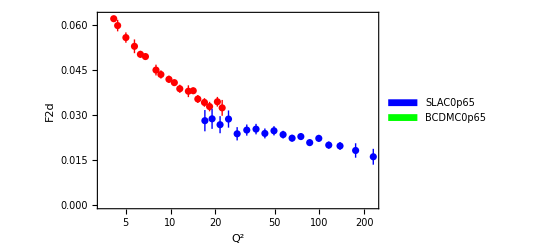

```mathematica
fig2=ErrorListLogLinearPlot[{SLACf2d,BCMCDf2d},PlotRange->All,Frame->True,FrameLabel->{"Q^2","F2d"},PlotStyle->{Directive[Thick,Red],Directive[Thick,Blue],Directive[Thick,Green]}];

Legended[fig2,Placed[SwatchLegend[{Directive[Thick,Blue],Directive[Thick,Green]},{"SLAC0p65","BCDMC0p65"}],{Right,Top}]]
```

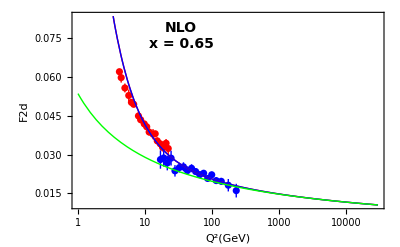

```mathematica
Show[fig2,fig55,PlotRange->All];
Legended[Show[fig2,fig55,PlotRange->All,Frame->True,FrameLabel->{"\!\(\*SuperscriptBox[\(Q\), \(2\)]\)(GeV)","F2d"},Epilog->{Text[Style["NLO",14,Bold],Scaled[{0.35,0.92}]],Text[Style["x = 0.65",14,Bold],Scaled[{0.35,0.84}]]}],Placed[SwatchLegend[{Directive[Thick,Red],Directive[Thick,Blue],Directive[Thick,Green]},{"SLAC0p65","BCDMC0p65"}],{Right,Top}]]
```

```mathematica
F2ns=(1/3( uvn-dvn)+2/3((3.3134127284740645*^8 Gamma[0.18682401890222378+1. s])/Gamma[13.040579290820865+1. s]-(1.2655096657044568*^13 Gamma[1.1868240189022239+1. s])/Gamma[14.040579290820865+1. s]+(1.2659068211018037*^13 Gamma[1.1869464534241143+1. s])/Gamma[14.040701725342757+1. s])mnsNLO)(1+ta/(4 Pi) c2nlo  );
```

```mathematica
Needs["ErrorBarLogPlots`"]
x=.
Nmax=.
Nmax=9;
α=3;
β=0.5;
θ=√((k!(2  k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!x^β(1-x)^α)D[(x^(β+k)(1-x)^(α+k)), {x,k}];
ckj=√((k! (2 k+α+β+1) Gamma[k+α+β+1])/(Gamma[k+α+1]Gamma[k+β+1]))(-1)^k/(k!)1/(j!)(Pochhammer[-k,j]Pochhammer[α+β+k+1,j]Pochhammer[β+j+1,k-j]);Momentg1NLOF2ns=(F2ns)/.s->j+1;

aαβns[k_]:=∑_(j=0)^k ckj*Momentg1NLOF2ns;

F2nsxQ=x^β(1-x)^α*(∑_(k=0)^Nmax θ*aαβns[k]);
```

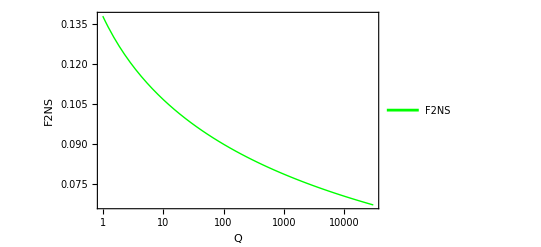

```mathematica
fig88=LogLinearPlot[{F2nsxQ/. x->0.275/. f->4},{Q,1,30000},Frame->True,FrameLabel->{"Q","F2NS"},PlotStyle->{Directive[Thick,Green]},PlotLegends->Placed[{"F2NS"},{Right,Top}]]
```

```mathematica
BCDMSf2NS={{13.25,0.08528,0.012616998},{15,0.11608,0.011657782},{17,0.12322,0.011708129},{19,0.10816,0.012417017},{21.5,0.1254,0.01131542},{24.5,0.0962,0.008213388},{28,0.09672,0.006301132},{32.5,0.099,0.005969675},{37.5,0.11376,0.005313116},{43,0.09988,0.005322506},{49.5,0.0949,0.006094902},{57,0.11454,0.005747315},{65.5,0.08588,0.007008487},{75,0.11814,0.007513644},{86,0.0971,0.011724121},{99,0.08828,0.015015103},{115.5,0.12018,0.016189424}}
```

{{13.25,0.08528,0.012617},{15,0.11608,0.0116578},{17,0.12322,0.0117081},{19,0.10816,0.012417},{21.5,0.1254,0.0113154},{24.5,0.0962,0.00821339},{28,0.09672,0.00630113},{32.5,0.099,0.00596968},{37.5,0.11376,0.00531312},{43,0.09988,0.00532251},{49.5,0.0949,0.0060949},{57,0.11454,0.00574732},{65.5,0.08588,0.00700849},{75,0.11814,0.00751364},{86,0.0971,0.0117241},{99,0.08828,0.0150151},{115.5,0.12018,0.0161894}}

```mathematica
nmcf2N={{3.5,0.0698,0.029789638},{4.5,0.076,0.021067101},{5.5,0.0902,0.019774497},{7,0.1108,0.016658158},{9,0.112,0.022146442},{11.5,0.0774,0.020807224},{15,0.0988,0.020781347},{20,0.0962,0.014333424},{27,0.0722,0.013671433},{36,0.1012,0.016284717},{48,0.0834,0.02248395},{65,0.0366,0.048585861}}
```

{{3.5,0.0698,0.0297896},{4.5,0.076,0.0210671},{5.5,0.0902,0.0197745},{7,0.1108,0.0166582},{9,0.112,0.0221464},{11.5,0.0774,0.0208072},{15,0.0988,0.0207813},{20,0.0962,0.0143334},{27,0.0722,0.0136714},{36,0.1012,0.0162847},{48,0.0834,0.022484},{65,0.0366,0.0485859}}

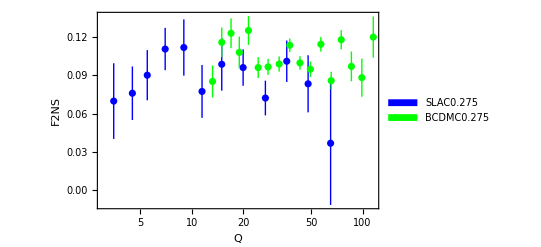

```mathematica
fig3=ErrorListLogLinearPlot[{nmcf2N,BCDMSf2NS},PlotRange->All,Frame->True,FrameLabel->{"Q","F2NS"},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Green]}];

Legended[fig3,Placed[SwatchLegend[{Directive[Thick,Blue],Directive[Thick,Green]},{"SLAC0.275","BCDMC0.275"}],{Right,Top}]]
```

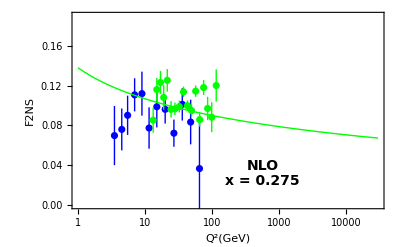

```mathematica
Show[fig3,fig55,PlotRange->All];
Legended[Show[fig3,fig88,PlotRange->{Automatic,{0,0.19}},Frame->True,FrameLabel->{"\!\(\*SuperscriptBox[\(Q\), \(2\)]\)(GeV)","F2NS"},Epilog->{Text[Style["NLO",14,Bold],Scaled[{0.61,0.22}]],Text[Style["x = 0.275",14,Bold],Scaled[{0.61,0.14}]]}],Placed[SwatchLegend[{Directive[Thick,Red],Directive[Thick,Blue]},{"SLAC0p65","BCDMC0p65"}],{Right,Top}]]
```